# Logistic regression

## Sigmoid function

```mathematica
Sigmoid[z_]:=1/(1+Exp[-z]);
```

```mathematica
{#,N@Sigmoid[#]}&/@Range[-5,5]//TableForm
```

-5 | 0.00669285
-4 | 0.0179862
-3 | 0.0474259
-2 | 0.119203
-1 | 0.268941
0 | 0.5
1 | 0.731059
2 | 0.880797
3 | 0.952574
4 | 0.982014
5 | 0.993307

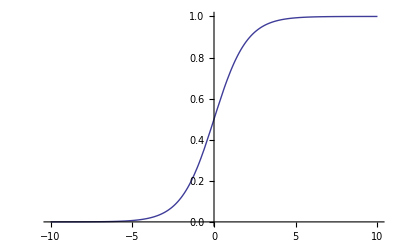

```mathematica
Plot[Sigmoid[x],{x,-10,10}]
```

```mathematica
range=5;
```

```mathematica
$opts={
Mesh->Join[ {Table[{x,Directive[Gray,Dashed]},{x,-range,+range}],Table[{x,Directive[Gray,Dashed]},{x,-range,range}]},{{{0,Directive[Blue]}},{{0,Directive[Red]}}},2],
ColorFunction-> ColorData["DarkRainbow"],
ImageSize-> 600
};
```

```mathematica
Plot3D[Abs[Sigmoid[x+I y]],{x,-range,range},{y,-range,range},AxesLabel->(Style[#,Large]&/@{"Re[z]","Im[z]","Abs[Sigmoid[z]]"}),Evaluate[$opts]]
```

-Graphics3D-

```mathematica
Plot3D[Re[Sigmoid[x+I y]],{x,-range,range},{y,-range,range},AxesLabel->(Style[#,Large]&/@{"Re[z]","Im[z]","Re[Sigmoid[z]]"}), Evaluate[$opts]]
Plot3D[Im[Sigmoid[x+I y]],{x,-range,range},{y,-range,range},AxesLabel->(Style[#,Large]&/@{"Re[z]","Im[z]","Im[Sigmoid[z]]"}),Evaluate[$opts]]
```

-Graphics3D-

-Graphics3D-

## Binary linear logistic regression

### Example data

There are two data files in CSV format.

```mathematica
$dataFile1=ToFileName[{NotebookDirectory[]},"ex2data1.txt"];
$dataFile2=ToFileName[{NotebookDirectory[]},"ex2data2.txt"];
```

The data files happen to be CSV file, import as so.

```mathematica
data1=Import[$dataFile1,"CSV"];
data2=Import[$dataFile2,"CSV"];
```

```mathematica
ex1=data1[[All,{1,2}]];
```

```mathematica
X1=Prepend[#,1]&/@ex1;
y1=data1[[All,3]];
```

```mathematica
X1//RandomChoice
```

{1,80.1902,44.8216}

Visualize the feature matrix X:

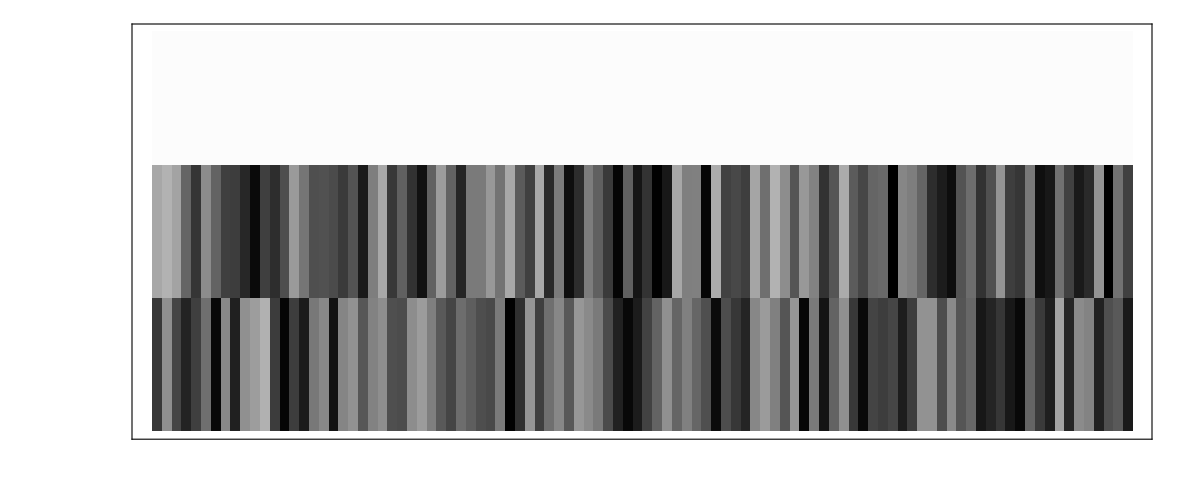

```mathematica
X1//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

Find the data points in the “admitted” and “not admitted” types:

```mathematica
ex1Admitted=Cases[data1,{x_,y_,1}:> {x,y}];
ex1NotAdmitted=Cases[data1,{x_,y_,0}:> {x,y}];
```

Plot it in the parameter space to get an idea of distribution:

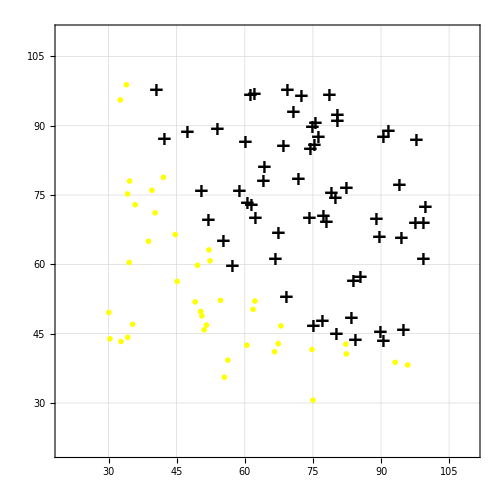

```mathematica
plotTrainingData1=ListPlot[{ex1Admitted,ex1NotAdmitted},
ImageSize-> 500,AspectRatio-> 1,
Frame-> True,GridLines-> Automatic,PlotRange-> {{20,110},{20,110}},
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]}
]
```

### Cost function

Hypothesis function h as a function of fitting parameter and feature matrix:

```mathematica
h[β_,X_]:=Sigmoid[X.β];
```

Cost function J as a function of fitting parameter and the example data set including the feature matrix X and the observed dependent variable y:

```mathematica
J[β_,X_,y_]:=-1/Length[y](y.Log[h[β,X]]+(1-y).Log[1-h[β,X]])
```

Define the fitting parameter in to the vector with right dimension:

```mathematica
Clear[β]
β=Table[Symbol["β"<>ToString[j]],{j,0,Length[X1[[1]]]-1}]
```

{β0,β1,β2}

Cost function at {0, 0, 0}

```mathematica
J[{0,0,0},X1,y1]
```

0.693147

### Find β to minimize cost function

#### Use NMinimize

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}

```mathematica
NMinimize[J[{β0,β1,β2},X1,y1],{β0,β1,β2}];
```

NMinimize::nnum: The function value Indeterminate is not a number at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}.

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res=NMinimize[regularize@J[{β0,β1,β2},X1,y1],{β0,β1,β2}];//AbsoluteTiming
```

{0.809698,Null}

```mathematica
res
```

{0.203498,{β0→-25.1613,β1→0.206232,β2→0.201472}}

#### Use FindMinimum

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}

```mathematica
FindMinimum[J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}]
```

FindMinimum::nrnum: The function value Indeterminate is not a real number at {β0, β1, β2} = {0.00303682, 0.364698, 0.342032}.

{0.693147,{β0→0.,β1→0.,β2→0.}}

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res=FindMinimum[regularize@J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}];//AbsoluteTiming
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.044742,Null}

```mathematica
res
```

{0.693147,{β0→0.,β1→0.,β2→0.}}

```mathematica
res
```

{0.693147,{β0→0.,β1→0.,β2→0.}}

#### Use LogitModelFit

```mathematica
data=Join[X1,List/@y1,2];
```

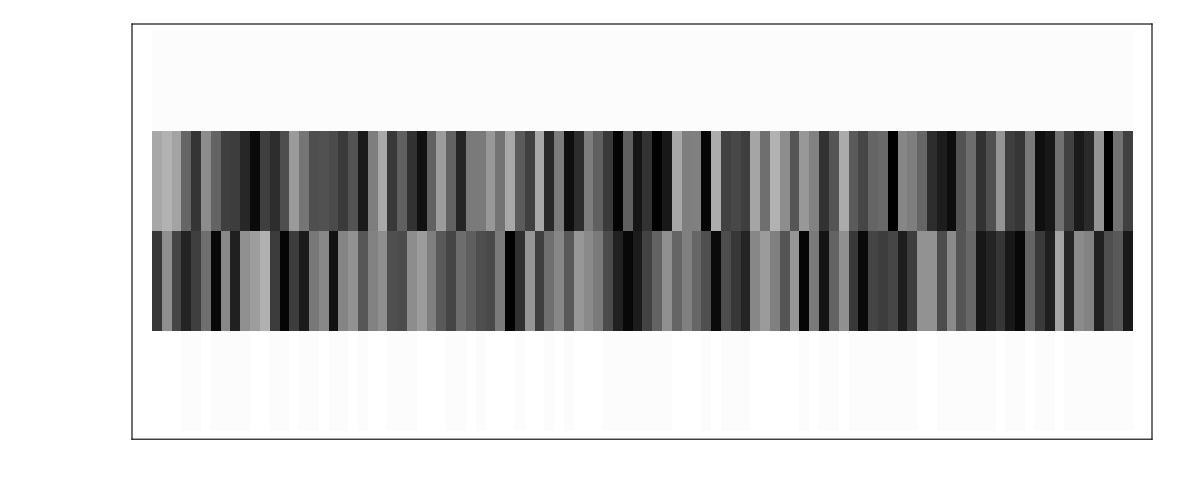

```mathematica
data//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logit1=LogitModelFit[data,{β0,β1,β2},{β0,β1,β2},IncludeConstantBasis-> False]
```

FittedModel[1/(1+ⅇ^(«1»))]

```mathematica
Normal[logit1]
```

1/(1+ⅇ^(25.1613 β0-0.206232 β1-0.201472 β2))

```mathematica
βFit=logit1["BestFitParameters"]
```

{-25.1613,0.206232,0.201472}

Include constant basis:

```mathematica
data=Join[ex1,List/@y1,2];
```

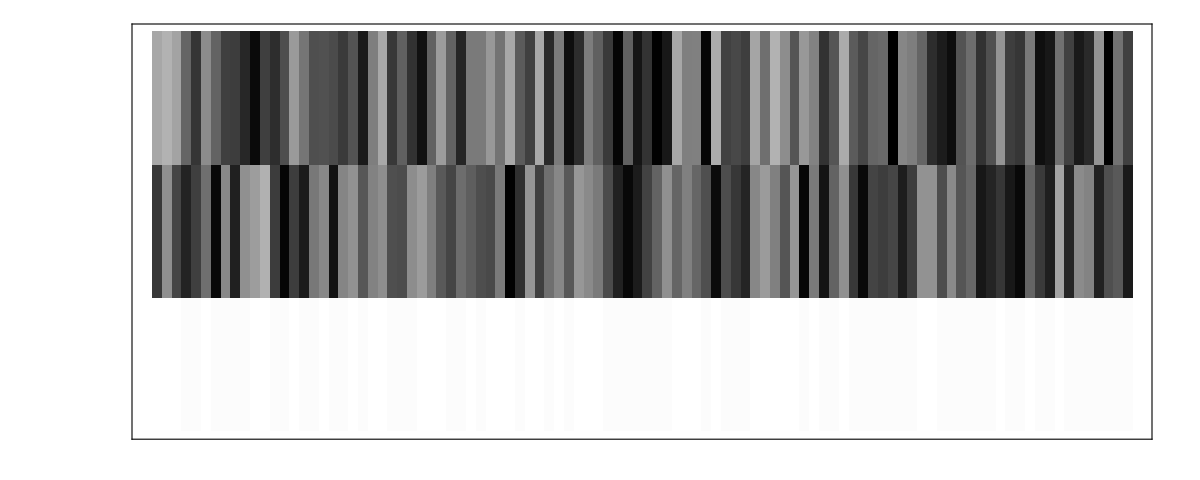

```mathematica
data//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logit2=LogitModelFit[data,{β1,β2},{β1,β2},IncludeConstantBasis-> True]
```

FittedModel[1/(1+ⅇ^(25.1613-«1»-«20» β2))]

```mathematica
Normal[logit2]
```

1/(1+ⅇ^(25.1613-0.206232 β1-0.201472 β2))

```mathematica
logit2["BestFitParameters"]
```

{-25.1613,0.206232,0.201472}

```mathematica
logit2["DevianceResiduals"]
```

{-0.436915,-0.00919343,-0.299673,0.138719,0.0600478,-0.147352,0.045219,1.31137,0.0240841,0.784037,-2.19287,-0.240888,0.0382131,0.0170918,-0.582489,0.196083,1.3033,-0.567618,0.024228,1.05322,-0.371949,0.0524155,-0.12203,-0.0142239,0.12771,0.559637,1.01028,-2.00192,-0.440317,-0.184239,0.465948,0.195677,-0.580195,1.36869,-0.39248,-0.259504,-1.95569,0.1582,-0.675486,-0.318908,0.245559,-0.110788,0.0328225,-1.18129,-0.0948556,-0.542896,0.118599,0.00276377,0.0398848,0.00429865,0.0615631,0.0316112,0.446772,-0.0749678,-0.130837,-0.329669,0.016934,-1.53832,0.170936,0.0925259,0.0306092,-0.0210903,-0.083804,-0.015942,-0.385626,-0.288912,0.338165,-0.142278,0.00975229,0.828825,-0.0111392,0.213837,0.0146046,0.495955,0.446216,0.00949699,0.414464,0.966662,-0.1787,-1.35275,0.0378883,0.23189,0.472132,1.78527,0.0108585,0.063554,-0.935759,0.018973,0.00731973,-0.475653,0.0105876,0.005436,-0.0533909,0.0368371,0.396046,0.552099,0.756977,0.0143805,1.47034,0.0223203}

Alternatively, use the GeneralizedLinearModelFit with ExponentialFamily → “Binomial”, LinkFunction→Automatic:

```mathematica
GeneralizedLinearModelFit [data,{β1,β2},{β1,β2},IncludeConstantBasis-> True,ExponentialFamily -> "Binomial", LinkFunction->Automatic]
```

FittedModel[1/(1+ⅇ^(25.1613-«1»-«20» β2))]

Examine deviance residuals:

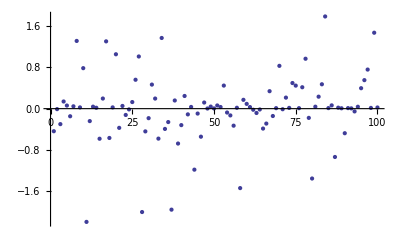

```mathematica
ListPlot[logit2["DevianceResiduals"]]
```

Cost function’s value at fitted parameters:

```mathematica
fittedParam=MapThread[Rule,{{β0,β1,β2},logit2["BestFitParameters"]}]
```

{β0→-25.1613,β1→0.206232,β2→0.201472}

```mathematica
J[{β0,β1,β2},X1,y1]/.fittedParam
```

0.203498

### Decision boundary

```mathematica
Total[βFit*{1,x1,x2}]==0
```

-25.1613+0.206232 x1+0.201472 x2==0

```mathematica
sol=Solve[Total[βFit*{1,x1,x2}]==0,x2]
```

{{x2→4.96348 (25.1613-0.206232 x1)}}

```mathematica
sol[[1,1,2]]
```

4.96348 (25.1613-0.206232 x1)

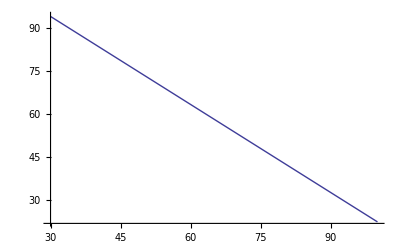

```mathematica
plotDecisionBoundary=Plot[sol[[1,1,2]],{x1,30,100}]
```

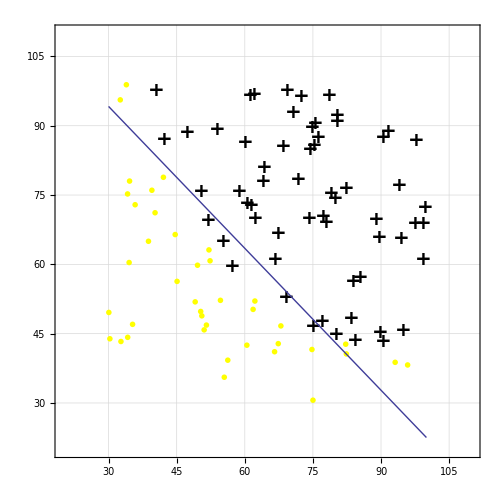

```mathematica
Show[{plotTrainingData1,plotDecisionBoundary}]
```

### Prediction

```mathematica
Normal[logit2]
```

1/(1+ⅇ^(25.1613-0.206232 β1-0.201472 β2))

```mathematica
predictedProb[x1_,x2_]:=Block[
{β1,β2,sol},
sol=MapThread[Rule,{{β1,β2},{x1,x2}}];
Normal[logit2]/.sol
]
```

```mathematica
predictedProb[45,85]
```

0.776291

### Prediction accuracy

```mathematica
predict[x1_,x2_]:=If[predictedProb[x1,x2]≥ 0.5,1,0]
```

```mathematica
Count[Map[predict@@#&,ex1]-y1,0]/Length[y1]//N
```

0.89

## Binary non-linear logistic regression

### Example data set

There are two data files in CSV format.

```mathematica
$dataFile=ToFileName[{NotebookDirectory[]},"ex2data2.txt"];
```

The data files happen to be CSV file, import as so.

```mathematica
data=Import[$dataFile,"CSV"];
```

```mathematica
featureData=data[[All,{1,2}]];
```

```mathematica
X=Prepend[#,1]&/@featureData;
y=data[[All,3]];
```

```mathematica
X//RandomChoice
```

{1,0.52938,-0.5212}

```mathematica
y//Length
```

118

Visualize the feature matrix X:

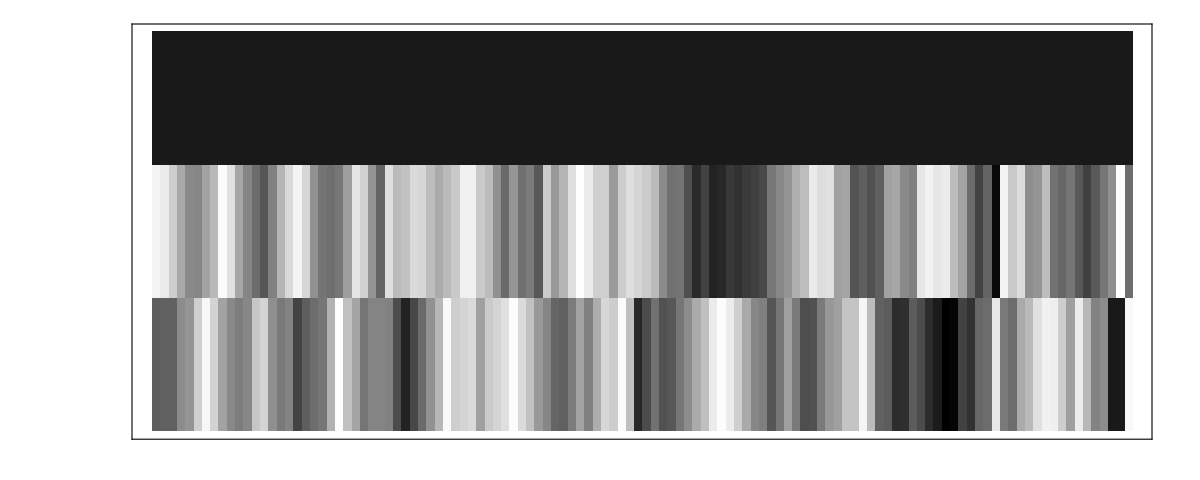

```mathematica
X//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

Find the data points in the “admitted” and “not admitted” types:

```mathematica
exAdmitted=Cases[data,{x_,y_,1}:> {x,y}];
exNotAdmitted=Cases[data,{x_,y_,0}:> {x,y}];
```

```mathematica
exAdmitted//RandomChoice
data//{Max[#],Min[#]}&
```

{-0.16187,0.8019}

{1.1089,-0.83007}

Plot it in the parameter space to get an idea of distribution:

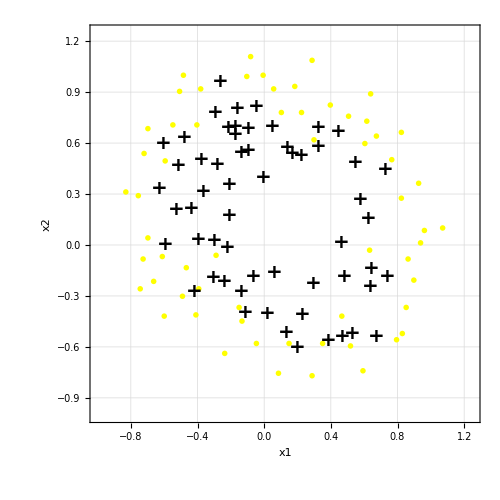

```mathematica
plotTrainingData=ListPlot[{Tooltip[#,#]&/@exAdmitted,Tooltip[#,#]&/@exNotAdmitted},
ImageSize-> 500,AspectRatio-> 1,
Frame-> True,GridLines-> Automatic,PlotRange-> {{-1,1.25},{-1,1.25}},
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]},
FrameLabel-> {"x1","x2"}
]
```

### Feature mapping: generating non-linear features from original features x1, x2

```mathematica
sortfun[expr_]:={Log[10,expr/.{x1-> 10,x2-> 10}],Log[10,expr/.{x1-> 1,x2-> 10}],Log[10,expr/.{x1-> 10,x2-> 1}]};
```

```mathematica
nonLinearFeatures=SortBy[Flatten[Table[Table[x1^p1 x2^p2,{p1,0,6-p2}],{p2,0,6}]],sortfun]
```

{1,x1,x2,x1^2,x1 x2,x2^2,x1^3,x1^2 x2,x1 x2^2,x2^3,x1^4,x1^3 x2,x1^2 x2^2,x1 x2^3,x2^4,x1^5,x1^4 x2,x1^3 x2^2,x1^2 x2^3,x1 x2^4,x2^5,x1^6,x1^5 x2,x1^4 x2^2,x1^3 x2^3,x1^2 x2^4,x1 x2^5,x2^6}

```mathematica
XNonlinear=Map[nonLinearFeatures/.#&,MapThread[Rule,{{x0,x1,x2},#}]&/@X];
```

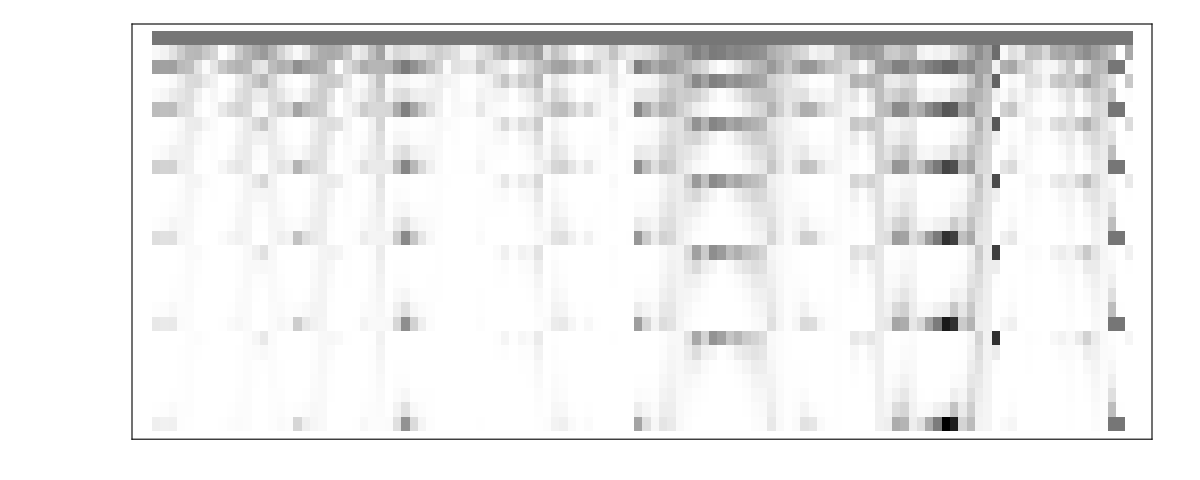

```mathematica
XNonlinear//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

### Cost function

Hypothesis function h as a function of fitting parameter and feature matrix:

```mathematica
h[β_,X_]:=Sigmoid[X.β];
```

Cost function J as a function of fitting parameter and the example data set including the feature matrix X and the observed dependent variable y:

```mathematica
J[β_,X_,y_]:=-1/Length[y](y.Log[h[β,X]]+(1-y).Log[1-h[β,X]])
```

Cost function J with regularization:

```mathematica
J[β_,X_,y_,λ_]:=-1/Length[y](y.Log[h[β,X]]+(1-y).Log[1-h[β,X]])+λ/(2*Length[y])β.β
```

Define the fitting parameter vector β and components with right dimension:

```mathematica
Clear[β]
β=Table[Symbol["β"<>ToString[j]],{j,0,Length[XNonlinear[[1]]]-1}]
```

{β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,β11,β12,β13,β14,β15,β16,β17,β18,β19,β20,β21,β22,β23,β24,β25,β26,β27}

Cost function at βInit = {0, 0, 0, ..., 0}

```mathematica
βInit=Table[0,{Length[XNonlinear[[1]]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
J[βInit,XNonlinear,y]
```

0.693147

```mathematica
λInit=1;
```

```mathematica
J[βInit,XNonlinear,y,λInit]
```

0.693147

### Find best fitting parameter vector β to minimize cost function J

#### Use NMinimize

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0,β1,β10,β11,β12,β13,β14,β15,β16,β17,β18,β19,β2,β20,β21,β22,β23,β24,β25,β26,β27,β3,β4,β5,β6,β7,β8,β9,λ} = {12.6559,18.8815,-29.085,-51.1986,29.671,16.936,-80.5918,-33.3686,-37.909,-32.1894,12.2811,50.7038,-23.9778,-28.0593,«18»,-18.4441,43.3584,59.3545,-63.1989,39.4808,-6.06265,-69.0835,-23.0398,35.274,-3.6493,24.3274,-77.6666,-24.3271,-72.0648}

```mathematica
res=TimeConstrained[NMinimize[J[β,XNonlinear,y,λInit],Evaluate[β],MaxIterations-> 1000],300];//AbsoluteTiming
```

{20.48482,Null}

Regularize J removing its singularities:

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res1=NMinimize[regularize@J[β,XNonlinear,y,0],Evaluate[β]];//AbsoluteTiming
res2=NMinimize[regularize@J[β,XNonlinear,y,1],Evaluate[β]];//AbsoluteTiming
res3=NMinimize[regularize@J[β,XNonlinear,y,10],Evaluate[β]];//AbsoluteTiming
res4=NMinimize[regularize@J[β,XNonlinear,y,100],Evaluate[β]];//AbsoluteTiming
```

{35.21606,Null}

{11.82945,Null}

{12.18284,Null}

{11.36455,Null}

```mathematica
res
```

{0.488609,{β0→1.57598,β1→0.941082,β2→1.64793,β3→-2.54345,β4→-1.48168,β5→-1.93056,β6→0.276247,β7→-0.572961,β8→-0.489843,β9→-0.192497,β10→-1.94876,β11→-0.01234,β12→-0.89423,β13→-0.462976,β14→-1.60822,β15→-0.302924,β16→-0.29724,β17→0.00166113,β18→-0.440167,β19→-0.471543,β20→-0.491892,β21→-1.43162,β22→0.0876229,β23→-0.419758,β24→0.058047,β25→-0.493705,β26→-0.266103,β27→-1.15368}}

```mathematica
JMinNMinimize1=res1[[1]]
βFitNMinimize1=res1[[2]]

JMinNMinimize2=res2[[1]]
βFitNMinimize2=res2[[2]]

JMinNMinimize3=res3[[1]]
βFitNMinimize3=res3[[2]]

JMinNMinimize4=res4[[1]]
βFitNMinimize4=res4[[2]]
```

0.21929

{β0→38.2304,β1→55.5954,β2→98.1463,β3→-369.425,β4→-177.117,β5→-194.258,β6→-366.005,β7→-842.205,β8→-719.445,β9→-511.894,β10→1182.68,β11→1279.32,β12→1907.87,β13→914.306,β14→514.275,β15→573.217,β16→1629.74,β17→2553.59,β18→2919.06,β19→1780.61,β20→785.316,β21→-1257.9,β22→-2259.98,β23→-4142.75,β24→-4290.55,β25→-4229.62,β26→-2055.54,β27→-750.38}

0.53516

{β0→1.14213,β1→0.601321,β2→1.16718,β3→-1.87175,β4→-0.915734,β5→-1.26953,β6→0.126683,β7→-0.368731,β8→-0.345184,β9→-0.173776,β10→-1.42386,β11→-0.0485564,β12→-0.60642,β13→-0.269318,β14→-1.16316,β15→-0.243101,β16→-0.207074,β17→-0.0431849,β18→-0.280281,β19→-0.286956,β20→-0.469105,β21→-1.03618,β22→0.0292351,β23→-0.292622,β24→0.0173668,β25→-0.328972,β26→-0.13796,β27→-0.93199}

0.651183

{β0→0.214714,β1→-0.00759425,β2→0.176096,β3→-0.40128,β4→-0.117449,β5→-0.231877,β6→-0.06668,β7→-0.0558426,β8→-0.0621443,β9→-0.0971232,β10→-0.317666,β11→-0.0146807,β12→-0.109129,β13→-0.0301429,β14→-0.267653,β15→-0.11187,β16→-0.0362743,β17→-0.0211449,β18→-0.0475364,β19→-0.0403769,β20→-0.181202,β21→-0.243089,β22→-0.00364207,β23→-0.0552512,β24→-0.00101445,β25→-0.060939,β26→-0.0129385,β27→-0.262898}

0.686527

{β0→0.00468639,β1→-0.0172685,β2→0.00641957,β3→-0.0540267,β4→-0.0132756,β5→-0.0372715,β6→-0.0182119,β7→-0.0076104,β8→-0.0088531,β9→-0.0222457,β10→-0.0428837,β11→-0.00238587,β12→-0.013932,β13→-0.00354833,β14→-0.0407238,β15→-0.0207857,β16→-0.00467205,β17→-0.00354981,β18→-0.00624897,β19→-0.00500396,β20→-0.0315315,β21→-0.0338151,β22→-0.00108319,β23→-0.00694194,β24→-0.000394504,β25→-0.00788596,β26→-0.00157686,β27→-0.0405885}

#### Use FindMinimum

Using NMinimize naively doesn’t work well as it doesn’t can give FindMinimum::lstol error when it fails to find a direction with sufficient decrease in the function to be minimized

```mathematica
resFindMinimum=FindMinimum[J[Evaluate[β],XNonlinear,y],Evaluate[Sequence@@({#,0}&/@Evaluate[β])],MaxIterations->400]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.21929,{β0→38.2308,β1→55.5958,β2→98.1467,β3→-369.43,β4→-177.12,β5→-194.261,β6→-366.009,β7→-842.211,β8→-719.448,β9→-511.895,β10→1182.7,β11→1279.34,β12→1907.9,β13→914.319,β14→514.28,β15→573.223,β16→1629.75,β17→2553.6,β18→2919.07,β19→1780.61,β20→785.315,β21→-1257.91,β22→-2260.01,β23→-4142.8,β24→-4290.59,β25→-4229.65,β26→-2055.55,β27→-750.381}}

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
resFindMinimum=FindMinimum[regularize@J[Evaluate[β],XNonlinear,y],Evaluate[Sequence@@({#,0}&/@Evaluate[β])]];//AbsoluteTiming
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{7.130128,Null}

```mathematica
res
```

{0.488609,{β0→1.57598,β1→0.941082,β2→1.64793,β3→-2.54345,β4→-1.48168,β5→-1.93056,β6→0.276247,β7→-0.572961,β8→-0.489843,β9→-0.192497,β10→-1.94876,β11→-0.01234,β12→-0.89423,β13→-0.462976,β14→-1.60822,β15→-0.302924,β16→-0.29724,β17→0.00166113,β18→-0.440167,β19→-0.471543,β20→-0.491892,β21→-1.43162,β22→0.0876229,β23→-0.419758,β24→0.058047,β25→-0.493705,β26→-0.266103,β27→-1.15368}}

#### Use LogitModelFit without constant basis

Define design matrix with non-linear features and response values:

```mathematica
designMatrix=Join[XNonlinear,List/@y,2];
```

```mathematica
designMatrix//RandomChoice
%//Length
```

{1,-0.49021,-0.3019,0.240306,0.147994,0.0911436,-0.1178,-0.0725483,-0.0446795,-0.0275163,0.0577469,0.0355639,0.0219023,0.0134887,0.00830716,-0.0283081,-0.0174338,-0.0107367,-0.00661232,-0.00407225,-0.00250793,0.0138769,0.00854622,0.00526326,0.00324142,0.00199626,0.00122941,0.000757144,0}

29

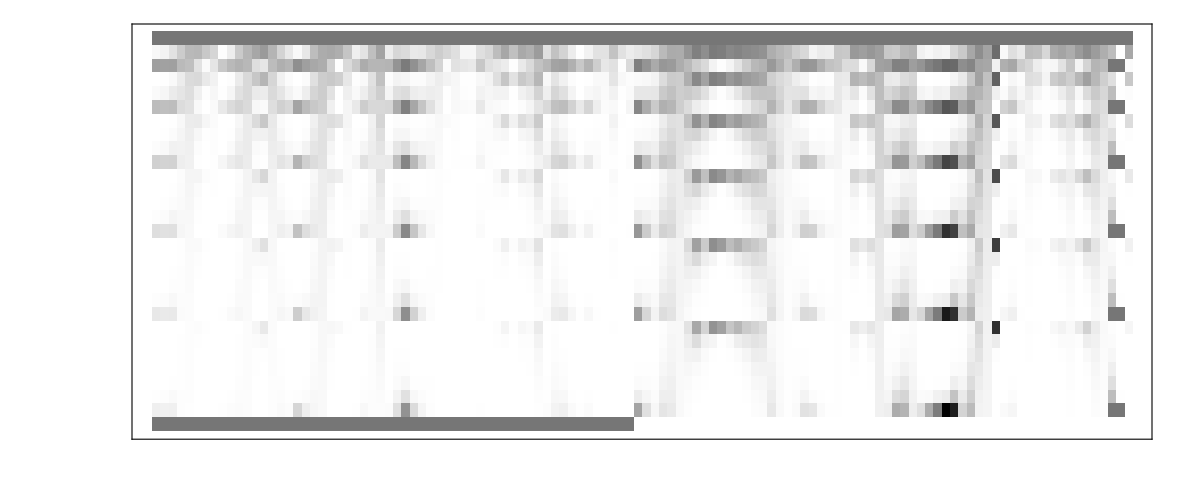

```mathematica
designMatrix//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

Define the feature variables χ:

```mathematica
Clear[χ]
χ=Table[Symbol["χ"<> ToString[i]],{i,0,Length[nonLinearFeatures]-1}]
```

{χ0,χ1,χ2,χ3,χ4,χ5,χ6,χ7,χ8,χ9,χ10,χ11,χ12,χ13,χ14,χ15,χ16,χ17,χ18,χ19,χ20,χ21,χ22,χ23,χ24,χ25,χ26,χ27}

```mathematica
logitModel1=LogitModelFit[designMatrix,Evaluate[χ],Evaluate[χ],IncludeConstantBasis-> False];//AbsoluteTiming
logitModel1
```

{0.16263,Null}

FittedModel[1/(1+ⅇ^(«40»+«1»))]

```mathematica
Normal[logitModel1]
```

1/(1+ⅇ^(-38.2308 χ0-55.5958 χ1-1182.7 χ10-1279.34 χ11-1907.9 χ12-914.319 χ13-514.28 χ14-573.223 χ15-1629.75 χ16-2553.6 χ17-2919.07 χ18-1780.61 χ19-98.1467 χ2-785.315 χ20+1257.91 χ21+2260.01 χ22+4142.8 χ23+4290.59 χ24+4229.65 χ25+2055.55 χ26+750.381 χ27+369.43 χ3+177.12 χ4+194.261 χ5+366.009 χ6+842.211 χ7+719.448 χ8+511.895 χ9))

```mathematica
βFitLogitModel1=MapThread[Rule,{Evaluate[β],logitModel1["BestFitParameters"]}]
```

{β0→38.2308,β1→55.5958,β2→98.1467,β3→-369.43,β4→-177.12,β5→-194.261,β6→-366.009,β7→-842.211,β8→-719.448,β9→-511.895,β10→1182.7,β11→1279.34,β12→1907.9,β13→914.319,β14→514.28,β15→573.223,β16→1629.75,β17→2553.6,β18→2919.07,β19→1780.61,β20→785.315,β21→-1257.91,β22→-2260.01,β23→-4142.8,β24→-4290.59,β25→-4229.65,β26→-2055.55,β27→-750.381}

#### Use LogitModelFit including constant basis

Include constant basis:

```mathematica
designMatrix=Join[XNonlinear[[All,2;;]],List/@y,2];
```

```mathematica
designMatrix[[1]]//Length
```

28

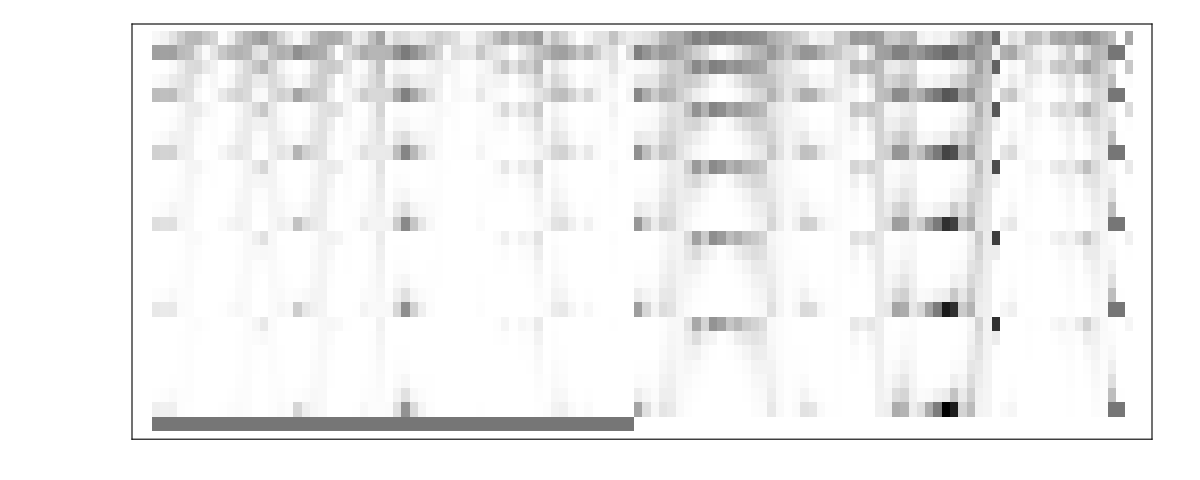

```mathematica
designMatrix//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logitModel2=LogitModelFit[designMatrix,Evaluate[χ[[2;;]]],Evaluate[χ[[2;;]]],IncludeConstantBasis-> True]
```

FittedModel[1/(1+ⅇ^(«40»+«19» χ9))]

```mathematica
Normal[logitModel2]
```

1/(1+ⅇ^(-38.2308-55.5958 χ1-1182.7 χ10-1279.34 χ11-1907.9 χ12-914.319 χ13-514.28 χ14-573.223 χ15-1629.75 χ16-2553.6 χ17-2919.07 χ18-1780.61 χ19-98.1467 χ2-785.315 χ20+1257.91 χ21+2260.01 χ22+4142.8 χ23+4290.59 χ24+4229.65 χ25+2055.55 χ26+750.381 χ27+369.43 χ3+177.12 χ4+194.261 χ5+366.009 χ6+842.211 χ7+719.448 χ8+511.895 χ9))

```mathematica
βFitLogitModel2=MapThread[Rule,{Evaluate[β],logitModel2["BestFitParameters"]}]
```

{β0→38.2308,β1→55.5958,β2→98.1467,β3→-369.43,β4→-177.12,β5→-194.261,β6→-366.009,β7→-842.211,β8→-719.448,β9→-511.895,β10→1182.7,β11→1279.34,β12→1907.9,β13→914.319,β14→514.28,β15→573.223,β16→1629.75,β17→2553.6,β18→2919.07,β19→1780.61,β20→785.315,β21→-1257.91,β22→-2260.01,β23→-4142.8,β24→-4290.59,β25→-4229.65,β26→-2055.55,β27→-750.381}

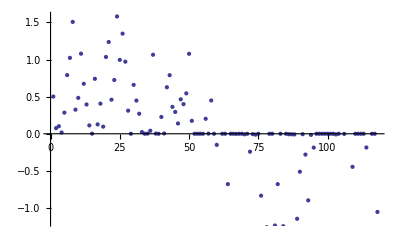

```mathematica
ListPlot@logitModel2["DevianceResiduals"]
```

#### Using GeneralizedLinearModelFit

Alternatively, use the GeneralizedLinearModelFit with ExponentialFamily → “Binomial”, LinkFunction→Automatic:

```mathematica
generalizedLinearModelFit=GeneralizedLinearModelFit [designMatrix,Evaluate[χ[[2;;]]],Evaluate[χ[[2;;]]],IncludeConstantBasis-> True,ExponentialFamily -> "Binomial", LinkFunction->Automatic]
```

FittedModel[1/(1+ⅇ^(«40»+«16» χ9))]

### Decision boundary

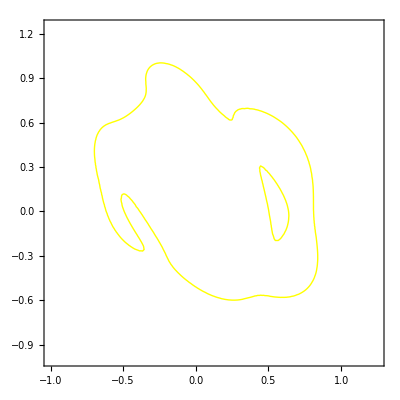

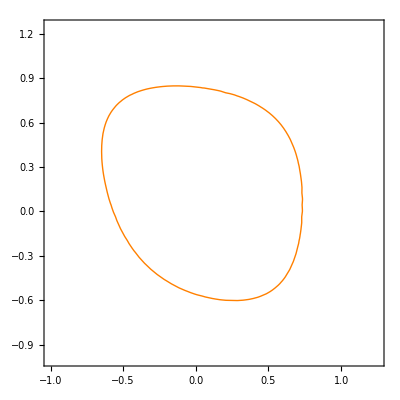

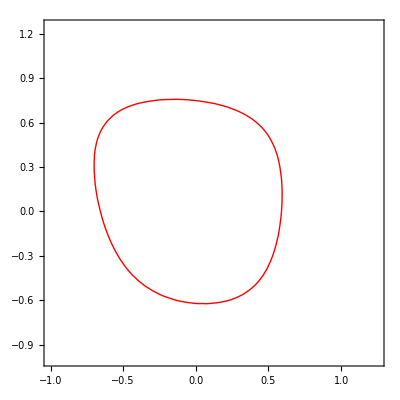

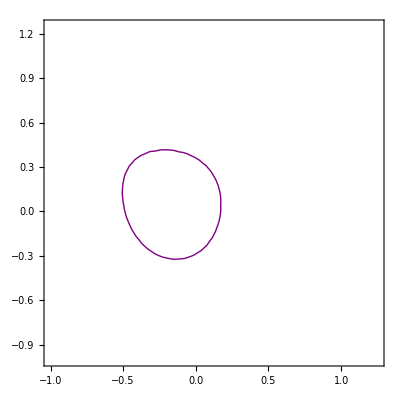

```mathematica
plotDecisionBoundaryFitNMinimize1=With[{βfit=βFitNMinimize1},ContourPlot[Total[Flatten[{βfit[[All,2]].nonLinearFeatures}]]==0,{x1,-1,1.25},{x2,-1,1.25},ContourStyle-> Yellow]]
plotDecisionBoundaryFitNMinimize2=With[{βfit=βFitNMinimize2},ContourPlot[Total[Flatten[{βfit[[All,2]].nonLinearFeatures}]]==0,{x1,-1,1.25},{x2,-1,1.25},ContourStyle-> Orange]]
plotDecisionBoundaryFitNMinimize3=With[{βfit=βFitNMinimize3},ContourPlot[Total[Flatten[{βfit[[All,2]].nonLinearFeatures}]]==0,{x1,-1,1.25},{x2,-1,1.25},ContourStyle-> Red]]
plotDecisionBoundaryFitNMinimize4=With[{βfit=βFitNMinimize4},ContourPlot[Total[Flatten[{βfit[[All,2]].nonLinearFeatures}]]==0,{x1,-1,1.25},{x2,-1,1.25},ContourStyle-> Purple]]
```

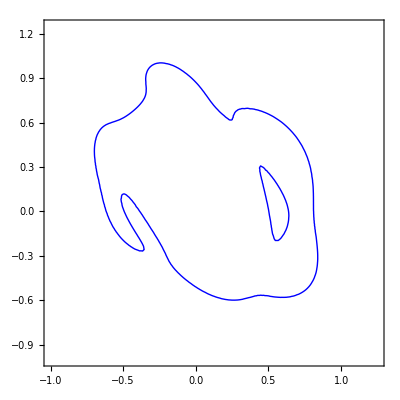

```mathematica
plotDecisionBoundaryLogitModel1=With[{βfit=βFitLogitModel1},ContourPlot[Total[Flatten[{βfit[[All,2]].nonLinearFeatures}]]==0,{x1,-1,1.25},{x2,-1,1.25},ContourStyle-> Blue]]
```

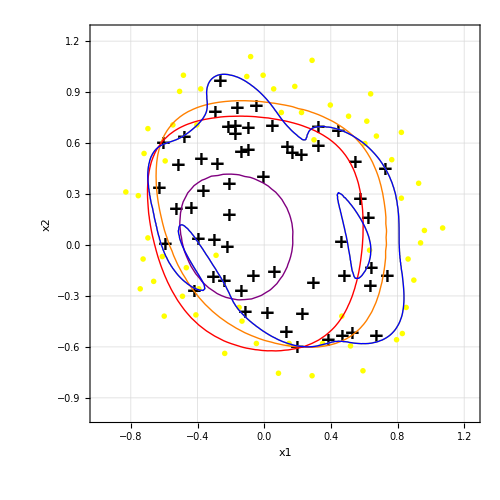

```mathematica
Show[{plotTrainingData,plotDecisionBoundaryFitNMinimize1,plotDecisionBoundaryFitNMinimize2,plotDecisionBoundaryFitNMinimize3,plotDecisionBoundaryFitNMinimize4,plotDecisionBoundaryLogitModel1}]
```

Mathematica’s built-in function LogitModelFit in this case find a decision boundary with a hole.  In terms of topology, the region contained within the blue boundary is not a simply connected space.

The decision boundary found by LogitModelFit and the one with λ=0 and NMinimize are almost same.

### Prediction

```mathematica
MapThread[Rule,{χ,nonLinearFeatures}]
```

{χ0→1,χ1→x1,χ2→x2,χ3→x1^2,χ4→x1 x2,χ5→x2^2,χ6→x1^3,χ7→x1^2 x2,χ8→x1 x2^2,χ9→x2^3,χ10→x1^4,χ11→x1^3 x2,χ12→x1^2 x2^2,χ13→x1 x2^3,χ14→x2^4,χ15→x1^5,χ16→x1^4 x2,χ17→x1^3 x2^2,χ18→x1^2 x2^3,χ19→x1 x2^4,χ20→x2^5,χ21→x1^6,χ22→x1^5 x2,χ23→x1^4 x2^2,χ24→x1^3 x2^3,χ25→x1^2 x2^4,χ26→x1 x2^5,χ27→x2^6}

```mathematica
predictedProb[xx1_,xx2_]:=Block[
{β1,β2,sol},
sol=ReplaceAll[MapThread[Rule,{χ,nonLinearFeatures}],{x1-> xx1,x2-> xx2}];
Normal[logitModel1]/.sol
]
```

```mathematica
data[[1]]
```

{0.051267,0.69956,1}

```mathematica
data[[1,{1,2}]]
```

{0.051267,0.69956}

```mathematica
predictedProb@@data[[1,{1,2}]]
```

0.881876

### Prediction accuracy

```mathematica
predict[x1_,x2_]:=If[predictedProb[x1,x2]≥ 0.5,1,0]
```

```mathematica
Count[Map[predict@@#&,featureData]-y,0]/Length[y]//N
```

0.889831

## Mathematica function reference

```mathematica
?LogitModelFit
```

RowBox[{"LogitModelFit", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] constructs a binomial logistic regression model of the form RowBox[{"1", "/", RowBox[{"(", RowBox[{"1", "+", SuperscriptBox["ⅇ", RowBox[{"-", RowBox[{"(", RowBox[{SubscriptBox["β", "0"], "+", RowBox[{SubscriptBox["β", "1"], SubscriptBox[StyleBox["f", "TI"], "1"]}], " ", "+", RowBox[{SubscriptBox["β", "2"], SubscriptBox[StyleBox["f", "TI"], "2"]}], " ", "+", "…"}], ")"}]}]]}], ")"}]}] that fits the SubscriptBox[StyleBox["y", "TI"], StyleBox["i", "TI"]] for successive StyleBox["x", "TI"] values 1, 2, StyleBox["…", "TR"].
RowBox[{"LogitModelFit", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["22", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] constructs a binomial logistic regression model of the form RowBox[{"1", "/", RowBox[{"(", RowBox[{"1", "+", SuperscriptBox["ⅇ", RowBox[{"-", RowBox[{"(", RowBox[{SubscriptBox["β", "0"], "+", RowBox[{SubscriptBox["β", "1"], SubscriptBox[StyleBox["f", "TI"], "1"]}], " ", "+", RowBox[{SubscriptBox["β", "2"], SubscriptBox[StyleBox["f", "TI"], "2"]}], " ", "+", "…"}], ")"}]}]]}], ")"}]}] where the SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] depend on the variables SubscriptBox[StyleBox["x", "TI"], StyleBox["k", "TI"]].
RowBox[{"LogitModelFit", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["v", "TI"]}], "}"}], "]"}] constructs a binomial logistic regression model from the design matrix StyleBox["m", "TI"] and response vector StyleBox["v", "TI"].

```mathematica
?IncludeConstantBasis
```

IncludeConstantBasis is an option for LinearModelFit and other fitting functions that specifies whether a constant term should be included if not explicitly given in the list of basis functions.

IncludeConstantBasis is an option for LinearModelFit and other fitting functions that specifies whether a constant term should be included if not explicitly given in the list of basis functions.

```mathematica
?ArrayPlot
```

RowBox[{"ArrayPlot", "[", StyleBox["array", "TI"], "]"}] generates a plot in which the values in an array are shown in a discrete array of squares.

```mathematica
?NMinimize
```

RowBox[{"NMinimize", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] minimizes StyleBox["f", "TI"] numerically with respect to StyleBox["x", "TI"].
RowBox[{"NMinimize", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] minimizes StyleBox["f", "TI"] numerically with respect to StyleBox["x", "TI"], StyleBox["y", "TI"], StyleBox["…", "TR"]. 
RowBox[{"NMinimize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] minimizes StyleBox["f", "TI"] numerically subject to the constraints StyleBox["cons", "TI"].

```mathematica
?ContourPlot
```

RowBox[{"ContourPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a contour plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "==", StyleBox["g", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots contour lines for which RowBox[{StyleBox["f", "TI"], "=", StyleBox["g", "TI"]}]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several contour lines.